## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_GAPD_typeIII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0.7,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
0.7 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,Overscript[(GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c, GAPD2],((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,Overscript[(GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c, GAPD4],((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
equivalentReactionsSetsList={};
simplifyFlag=True;
simplifyMaxTime=30;
inhibitionListSubset=inhibitionList;
otherMetsForwardZeroSub={};otherMetsReverseZeroSub={};
```

```mathematica
rxnMets =  Map[getID[#]&, Flatten[{getSubstrates[rxn], getProducts[rxn]}]];
	If[ !SameQ[inhibitionList, {}],
		inhibitors = inhibitionList[[All,3]];
		prodInhibBool = MemberQ[Map[MemberQ[rxnMets, #]&, inhibitors], True];,
		prodInhibBool = False;
	];
	
	{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
	rates = getEnzymeRates[enzymeModel];
	{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];
```

```mathematica
{allCatalyticReactions, nonCatalyticReactions} = classifyReactions[enzymeModel];
	
rateConstSubstitutionList = 
	If[TrueQ[MWCFlag],
		getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions],
		{}
	];
```

```mathematica
If[ !SameQ[equivalentReactionsSetsList, {}] && !SameQ[equivalentReactionsSetsList, Null],
			AppendTo[rateConstSubstitutionList, getHalfHaldaneSub[equivalentReactionsSetsList]];
			rateConstSubstitutionList = Flatten @ rateConstSubstitutionList;
	];
```

```mathematica
(*Identify Transition Rate Equations*)
transitionID = getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs = getTransitionRateEqs[transitionID, rates];
```

```mathematica
(*King-Altman Workaround UsingMathematicaSolve*)
	(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFluxNoProdInhib=
	If[prodInhibBool,
			Print["prod inhib"];
			getFluxEquation[inputPath, rxnName, enzymeModel, rateConstSubstitutionList, transitionRateEqs, simplifyFlag, simplifyMaxTime,nActiveSites, "NoProdInhibRefactor"],
			Null
	];
```

```mathematica
If[!SameQ[inhibitionListSubset,{}],
		{enzymeModel,nonCatalyticReactions} = addInhibitionReactions[enzymeModel,rxnName,inhibitionListSubset,allCatalyticReactions,nonCatalyticReactions];
];
```

```mathematica
absoluteFlux = getFluxEquation[inputPath, rxnName, enzymeModel, rateConstSubstitutionList, transitionRateEqs, simplifyFlag, simplifyMaxTime, nActiveSites, ""];
```

Generating flux equation...

{((GAPD^c&nad^c&g3p^c&pi^c)_^-((GAPD^c&nadh^c&(13dpg)^c)_^)/K_GAPD6) Volume_c k_GAPD6^⟶}

Volume_c (-(GAPD^c&nadh^c&(13dpg)^c)_^ k_GAPD6^⟵+(GAPD^c&nad^c&g3p^c&pi^c)_^ k_GAPD6^⟶)

1

2

3

0.792084

4

0.00139

5

0.00014

Simplifying...

6

0.30532

```mathematica
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse} = 
		getRateEqs[rxn, enzymeModel, absoluteFlux, rateConstSubstitutionList, reverseZeroSub, forwardZeroSub, volumeSub,
				metSatForSub, metSatRevSub, inputPath, absoluteFluxNoProdInhib, absoluteFluxNoProdInhib,
				otherMetsForwardZeroSub, otherMetsReverseZeroSub, simplifyFlag, simplifyMaxTime];
```

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

```mathematica
(* set up haldane relations *)
haldaneRatiosList  = Table[
				haldane = haldaneRelation[KeqName,catalyticReactionsSet]/.rateConstSubstitutionList;
				haldane[[2]],
		{catalyticReactionsSet, catalyticReactionsSetsList}] // DeleteDuplicates;
```

```mathematica
(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub} = 
			getMetRatesSubs[enzymeModel, haldaneRatiosList, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
							relativeRateReverse,KeqVal,otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

```mathematica
(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub} = 
		exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
						relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub,
						otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

```mathematica
KeqName
```

GAPD

```mathematica
KeqVal
```

K_GAPD

```mathematica
rateConstsSub
```

{k_GAPD1^⟵→x<0>,k_GAPD1^⟶→x<1>,k_GAPD2^⟵→x<2>,k_GAPD2^⟶→x<3>,k_GAPD3^⟵→x<4>,k_GAPD3^⟶→x<5>,k_GAPD4^⟵→x<6>,k_GAPD4^⟶→x<7>,k_GAPD5^⟵→x<8>,k_GAPD5^⟶→x<9>,k_GAPD6^⟵→x<10>,k_GAPD6^⟶→x<11>}

```mathematica
rates
```

{(-((GAPD^c&nad^c)_^)/K_GAPD1+(GAPD^c)_^ nad^c) Volume_c k_GAPD1^⟶,((GAPD^c&nadh^c)_^-((GAPD^c)_^ nadh^c)/K_GAPD2) Volume_c k_GAPD2^⟶,(-((GAPD^c&nad^c&g3p^c)_^)/K_GAPD3+(GAPD^c&nad^c)_^ g3p^c) Volume_c k_GAPD3^⟶,((GAPD^c&nadh^c&(13dpg)^c)_^-((GAPD^c&nadh^c)_^ (13dpg)^c)/K_GAPD4) Volume_c k_GAPD4^⟶,(-((GAPD^c&nad^c&g3p^c&pi^c)_^)/K_GAPD5+(GAPD^c&nad^c&g3p^c)_^ pi^c) Volume_c k_GAPD5^⟶,((GAPD^c&nad^c&g3p^c&pi^c)_^-((GAPD^c&nadh^c&(13dpg)^c)_^)/K_GAPD6) Volume_c k_GAPD6^⟶}

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, rateConstSubstitutionList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/customRatio_1.txt"	425.

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, rateConstSubstitutionList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
psoParameterPath
```

/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/input/psoParameters_GAPD_20178141612.txt

```mathematica
psoResultsFile
```

/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeIII/output/raw/psoResults_GAPD_20178141612.txt

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.09183297847
best_fit: 1.0451419661
best_fit: 1.07948143555
best_fit: 1.06055724968
best_fit: 1.00139758817

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | haldaneRatio_1 | 0.000247381 | 6.11972×10^-8 | 0.000257539 | 0.0569777 | 0.452 | 0.452258
1 | relRateFor_nad | 0.00196329 | 3.85452×10^-6 | 0.000410041 | 0.451045 | 0.0909091 | 0.0904991
1 | relRateFor_nad | 0.00186438 | 3.47593×10^-6 | 0.00058604 | 0.42837 | 0.136807 | 0.136221
1 | relRateFor_nad | 0.00172653 | 2.9809×10^-6 | 0.000796533 | 0.396759 | 0.20076 | 0.199963
1 | relRateFor_nad | 0.00154542 | 2.38832×10^-6 | 0.00101146 | 0.355214 | 0.284747 | 0.283736
1 | relRateFor_nad | 0.00132512 | 1.75594×10^-6 | 0.0011786 | 0.304655 | 0.386863 | 0.385685
1 | relRateFor_nad | 0.00108091 | 1.16837×10^-6 | 0.0012429 | 0.248579 | 0.5 | 0.498757
1 | relRateFor_nad | 0.000836564 | 6.99839×10^-7 | 0.00117992 | 0.192441 | 0.613137 | 0.611957
1 | relRateFor_nad | 0.000615902 | 3.79335×10^-7 | 0.00101363 | 0.141716 | 0.715253 | 0.714239
1 | relRateFor_nad | 0.00043433 | 1.88643×10^-7 | 0.000798906 | 0.0999583 | 0.79924 | 0.798441
1 | relRateFor_nad | 0.000296019 | 8.76274×10^-8 | 0.00058816 | 0.0681377 | 0.863193 | 0.862605
1 | relRateFor_nad | 0.000196729 | 3.87024×10^-8 | 0.000411712 | 0.0452883 | 0.909091 | 0.908679
0.7 | relRateFor_g3p | 0.0042853 | 0.0000183638 | 0.000892613 | 0.981875 | 0.0909091 | 0.0900165
0.7 | relRateFor_g3p | 0.00406996 | 0.0000165645 | 0.00127609 | 0.932765 | 0.136807 | 0.135531
0.7 | relRateFor_g3p | 0.00376972 | 0.0000142108 | 0.00173508 | 0.864254 | 0.20076 | 0.199025
0.7 | relRateFor_g3p | 0.00337512 | 0.0000113914 | 0.00220434 | 0.774138 | 0.284747 | 0.282543
0.7 | relRateFor_g3p | 0.00289486 | 8.38021×10^-6 | 0.00257012 | 0.66435 | 0.386863 | 0.384293
0.7 | relRateFor_g3p | 0.00236215 | 5.57974×10^-6 | 0.00271214 | 0.542428 | 0.5 | 0.497288
0.7 | relRateFor_g3p | 0.00182878 | 3.34443×10^-6 | 0.00257644 | 0.420206 | 0.613137 | 0.61056
0.7 | relRateFor_g3p | 0.0013468 | 1.81388×10^-6 | 0.00221466 | 0.309633 | 0.715253 | 0.713038
0.7 | relRateFor_g3p | 0.000949993 | 9.02487×10^-7 | 0.00174638 | 0.218505 | 0.79924 | 0.797494
0.7 | relRateFor_g3p | 0.000647594 | 4.19377×10^-7 | 0.00128618 | 0.149003 | 0.863193 | 0.861907
0.7 | relRateFor_g3p | 0.000430438 | 1.85277×10^-7 | 0.000900572 | 0.0990629 | 0.909091 | 0.90819
1 | relRateFor_pi | 0.00115561 | 1.33543×10^-6 | 0.000241577 | 0.265735 | 0.0909091 | 0.0906675
1 | relRateFor_pi | 0.00109734 | 1.20415×10^-6 | 0.000345235 | 0.252352 | 0.136807 | 0.136462
1 | relRateFor_pi | 0.00101613 | 1.03252×10^-6 | 0.000469175 | 0.233699 | 0.20076 | 0.200291
1 | relRateFor_pi | 0.000909464 | 8.27125×10^-7 | 0.000595671 | 0.209193 | 0.284747 | 0.284152
1 | relRateFor_pi | 0.000779737 | 6.0799×10^-7 | 0.000693956 | 0.17938 | 0.386863 | 0.386169
1 | relRateFor_pi | 0.000635965 | 4.04451×10^-7 | 0.000731645 | 0.146329 | 0.5 | 0.499268
1 | relRateFor_pi | 0.000492144 | 2.42206×10^-7 | 0.000694415 | 0.113256 | 0.613137 | 0.612442
1 | relRateFor_pi | 0.000362292 | 1.31256×10^-7 | 0.000596422 | 0.0833861 | 0.715253 | 0.714656
1 | relRateFor_pi | 0.000255464 | 6.52621×10^-8 | 0.000469998 | 0.0588056 | 0.79924 | 0.79877
1 | relRateFor_pi | 0.000174101 | 3.03112×10^-8 | 0.00034597 | 0.0400803 | 0.863193 | 0.862847
1 | relRateFor_pi | 0.000115699 | 1.33863×10^-8 | 0.000242156 | 0.0266372 | 0.909091 | 0.908849
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | absRateFor | 1.58073×10^-8 | 2.49872×10^-16 | 9.7546×10^-6 | 3.63978×10^-6 | 268 | 268.
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | KdRatio_nad | 0.128734 | 0.0165725 | 8.20882×10^-8 | 25.6526 | 3.2×10^-7 | 2.37912×10^-7
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998
1 | customRatio_1 | 1.60627×10^-6 | 2.5801×10^-12 | 0.00157189 | 0.000369856 | 425. | 424.998

### Simulated Data and Best Fit Data Plot

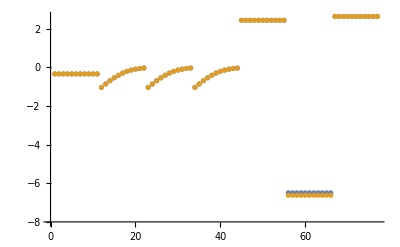

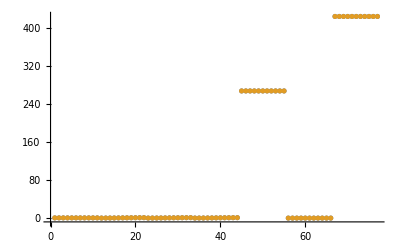

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

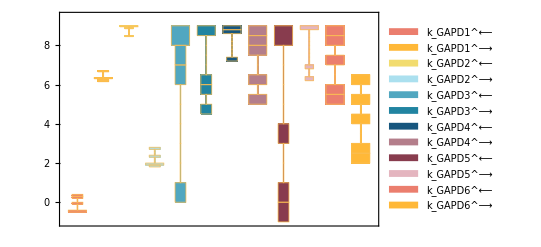

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

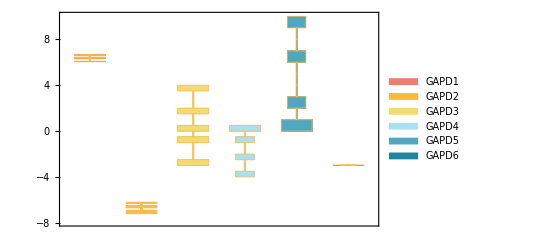

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

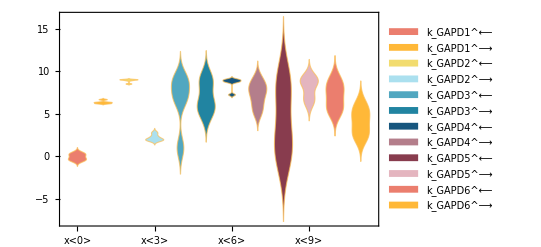

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

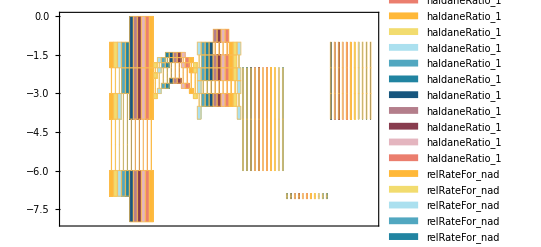

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000452243 | 0.498397
0.00089 | 0.000899708 | 1.09077
0.00053 | 0.000531553 | 0.293087

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 3.63978×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 424.998 | 0.000369856

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452258 | 0.0569777